Create a CAMB input file for the Planck13 LCDM cosmology:

```mathematica
Needs["DeepZot`CosmoTools`"]
```

```mathematica
createCosmology[Planck13]
```

```mathematica
SetDirectory["/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb/"]
```

/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb

```mathematica
exportToCamb["Planck13.camb",Planck13,redshifts->{0,1.2},kmax->100]
```

Planck13.camb

```mathematica
Needs["DeepZot`PowerTools`"]
```

```mathematica
Planck13Pk=makePower[ReadList["Planck13_matterpower_1.dat",Number,RecordLists->True]];
```

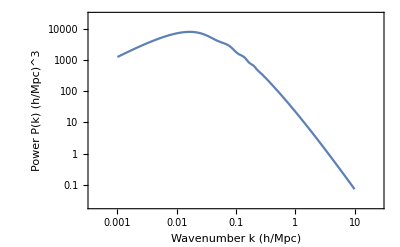

```mathematica
LogLogPlot[Planck13Pk[k],{k,0.001,10},GridLines->Automatic,Frame->True,FrameLabel->{"Wavenumber k (h/Mpc)","Power P(k) (h/Mpc)^3"}]
```

Create a log-normal power spectrum that roughly matches the Planck spectrum:

```mathematica
k0=0.0165;
P0=8000.0;
r0=3.2;
```

```mathematica
LogNormalPk[k_]:=P0 Exp[-Log[k/k0]^2/(2 Log[r0]^2)]
```

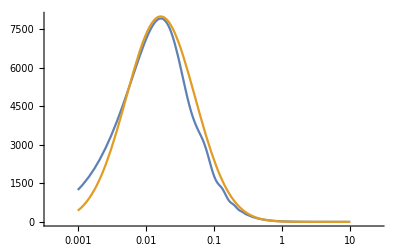

```mathematica
LogLinearPlot[{Planck13Pk[k],LogNormalPk[k]},{k,0.001,10}]
```

Compare the corresponding correlation functions:

```mathematica
{rmin,rmax,veps}={10,200,0.001};
Planck13Xi=sbTransform[Planck13Pk,rmin,rmax,0,veps];
LogNormalXi=sbTransform[LogNormalPk,rmin,rmax,0,veps];
```

```mathematica
Planck13Xi[100]
```

sbTransform[Function[Private`k$,Which[Private`k$≤Private`kmin$37175,Private`plo$37175[Private`k$],Private`k$≥Private`kmax$37175,Private`phi$37175[Private`k$],True,Private`interpolator$37175[Log[Private`k$]]]],10,200,0.001][100]

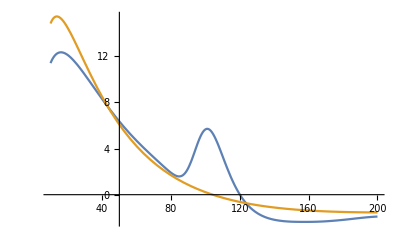

```mathematica
Plot[{r^2Planck13Xi[r],r^2 LogNormalXi[r]},{r,rmin,rmax}]
```